```mathematica
Lx=60;
Ly=60;
A=Lx*Ly;
```

```mathematica
m0 = 1;
```

```mathematica
LineChernListP1 = Import["/media/archisman/Home Partition/archisman/Documents/GitHub/quasicrystals/local_chern_number_data/data/datalocalChernLx=60Ly=60m0=1.dat"];
```

```mathematica
LineChernListP2 = LineChernListP1 = Import["/media/archisman/Home Partition/archisman/Documents/GitHub/quasicrystals/local_chern_number_data/data/datalocalChernLx=60Ly=60m0=-1.dat"];
```

```mathematica
SiteIndexList = Table[(Round[Ly/2]-1)*Lx + ii,{ii,1,Lx} ];
```

```mathematica
list1 = Table[LineChernListP1[[SiteIndexList[[ii]]]][[1]],{ii,1,Lx}]
```

{-25.6348,-0.0653543,-0.959296,0.877681,0.818942,0.985207,0.981911,0.998127,0.998095,0.999754,0.99979,0.999966,0.999976,0.999995,0.999997,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999997,0.999995,0.999976,0.999966,0.99979,0.999754,0.998095,0.998127,0.981911,0.985207,0.818942,0.877681,-0.959296,-0.0653543,-25.6348}

```mathematica
list2 = Table[LineChernListP2[[SiteIndexList[[ii]]]][[1]],{ii,1,Lx}]
```

{25.6348,0.0653543,0.959296,-0.877681,-0.818942,-0.985207,-0.981911,-0.998127,-0.998095,-0.999754,-0.99979,-0.999966,-0.999976,-0.999995,-0.999997,-0.999999,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-0.999999,-0.999997,-0.999995,-0.999976,-0.999966,-0.99979,-0.999754,-0.998095,-0.998127,-0.981911,-0.985207,-0.818942,-0.877681,0.959296,0.0653543,25.6348}

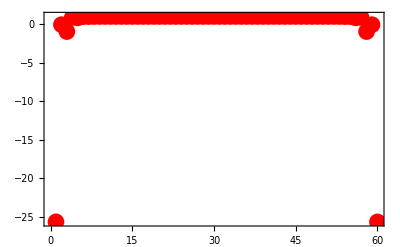

```mathematica
ListPlot[list1,PlotRange->All,Frame->True,PlotStyle-> {Red,PointSize[0.03]},Axes->False]
```

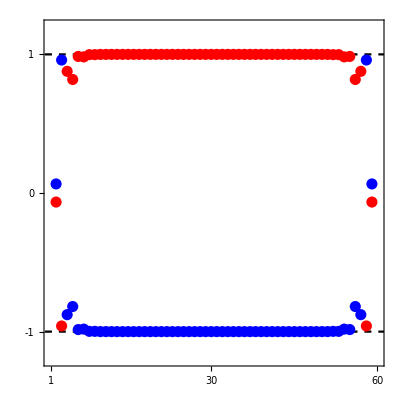

```mathematica
Show[Plot[1,{x,0,Lx+2},PlotStyle->{Dashed,Black},PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,Axes->False],
Plot[-1,{x,0,Lx+2},PlotStyle->{Dashed,Black},PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,Axes->False],
ListPlot[list1,PlotRange->{-1.2,1.2},Frame->True,PlotStyle-> {Red,PointSize[0.02]},Axes->False],
ListPlot[list2,PlotRange->{-1.2,1.2},Frame->True,PlotStyle-> {Blue,PointSize[0.02]},Axes->False],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 24,
FrameTicks->{ {{{-1,"-1"},{0,"0"},{1,"1"}},None},{{1,Lx/2,Lx},None}},
ImageSize-> 400,AspectRatio-> 1]
```